```mathematica
Quantity[15,"Minutes"]+Quantity[21,"Seconds"]
```

921 s

```mathematica
Quantity[921, "Seconds"]/2.5
```

368.4 s

```mathematica
UnitConvert[Quantity[368.40000000000003,"Seconds"],MixedUnit[{"Minutes","Seconds"}]]
```

6 8.4

```mathematica
a(1+r)^n
```

a (1+r)^n

```mathematica
a (1+r)^n==a(1+r)a(1+r)^(n-1)
```

a (1+r)^n==a^2 (1+r)^n

```mathematica
Reduce[a (1+r)^n==a^2 (1+r)^n]
```

a==0||a==1||(1+r)^n==0

```mathematica
a (1+r)^n==(1+r)a(1+r)^(n-1)
```

True

```mathematica
a(1+r)^(n-k)(1+r)^k
```

a (1+r)^n

```mathematica
(1-(1+Cos[π n])/2)(3n+1)+((1+Cos[π μ])/2)(n/2)
```

(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[π μ])

```mathematica
(1-(1+Cos[π n])/2)(3n+1)+((1+Cos[π n])/2)(n/2)
```

(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])

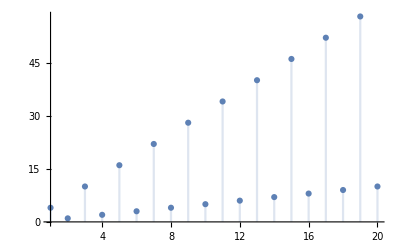

```mathematica
DiscretePlot[(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]),{n,1,20}]
```

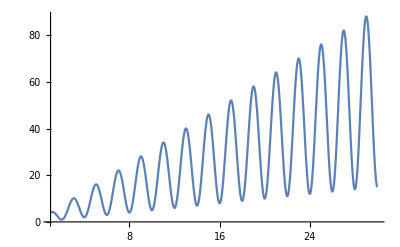

```mathematica
Plot
```

```mathematica
f[n_]:=(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])
```

```mathematica
NestList[f,n,4]
```

{n,(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]),(1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]),(1+3 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))) (1+1/2 (-1-Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))]))+1/4 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))])) (1+Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))]),(1+3 ((1+3 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))) (1+1/2 (-1-Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))]))+1/4 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))])) (1+Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))]))) (1+1/2 (-1-Cos[π ((1+3 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))) (1+1/2 (-1-Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))]))+1/4 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))])) (1+Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))]))]))+1/4 ((1+3 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))) (1+1/2 (-1-Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))]))+1/4 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))])) (1+Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))])) (1+Cos[π ((1+3 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))) (1+1/2 (-1-Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))]))+1/4 ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))])) (1+Cos[π ((1+3 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))) (1+1/2 (-1-Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))+1/4 ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])) (1+Cos[π ((1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]))]))]))])}

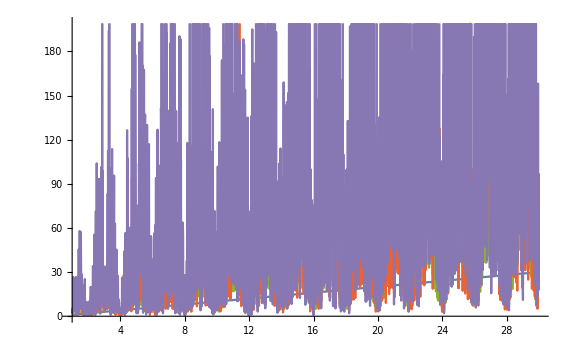

```mathematica
Plot[Out[14],{n,1,30}]
```

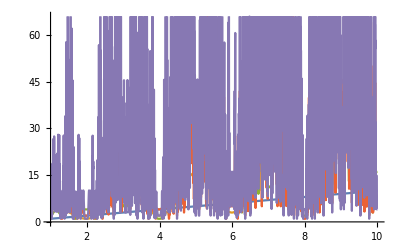

```mathematica
Plot[Out[14],{n,1,10}]
```

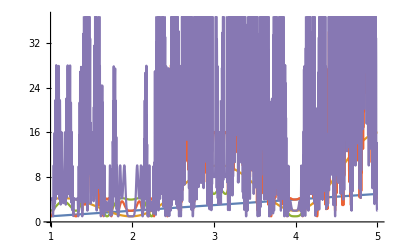

```mathematica
Plot[Out[14],{n,1,5}]
```

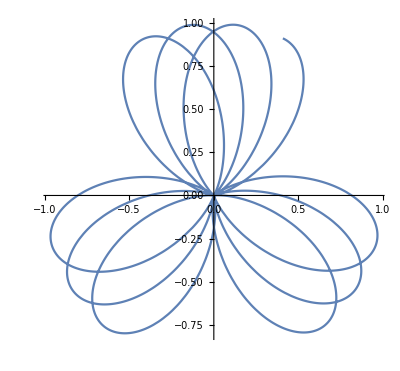

```mathematica
PolarPlot[(1+Cos[π θ])/2,{θ,1,20}]
```

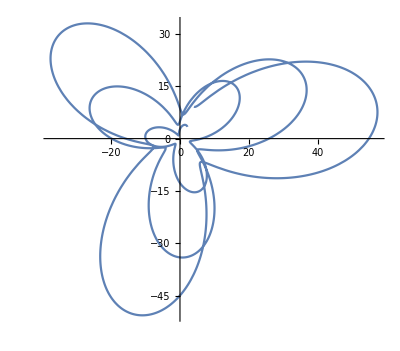

```mathematica
PolarPlot[(1+3 θ) (1+1/2 (-1-Cos[θ π]))+1/4 θ(1+Cos[θ π]),{θ,1,20}]
```

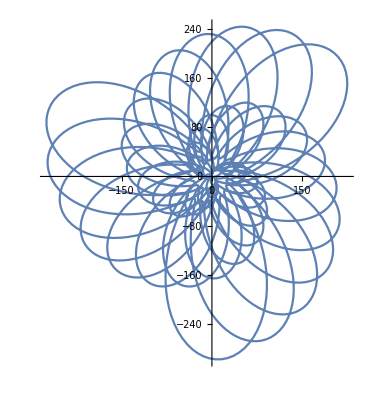

```mathematica
PolarPlot[(1+3 θ) (1+1/2 (-1-Cos[θ π]))+1/4 θ(1+Cos[θ π]),{θ,1,100}]
```

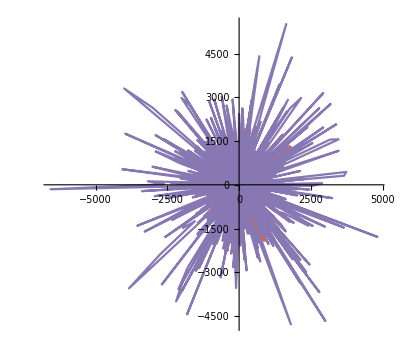

```mathematica
PolarPlot[Out[14],{n,1,100}]
```

```mathematica
PolarPlot[Out[14][{1}],{n,1,100}]
```

-Graphics-

```mathematica
NestList[f,θ,3]
```

{θ,(1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]),(1+3 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))) (1+1/2 (-1-Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))]))+1/4 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ])) (1+Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))]),(1+3 ((1+3 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))) (1+1/2 (-1-Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))]))+1/4 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ])) (1+Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))]))) (1+1/2 (-1-Cos[π ((1+3 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))) (1+1/2 (-1-Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))]))+1/4 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ])) (1+Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))]))]))+1/4 ((1+3 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))) (1+1/2 (-1-Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))]))+1/4 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ])) (1+Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))])) (1+Cos[π ((1+3 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))) (1+1/2 (-1-Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))]))+1/4 ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ])) (1+Cos[π ((1+3 θ) (1+1/2 (-1-Cos[π θ]))+1/4 θ (1+Cos[π θ]))]))])}

```mathematica
PolarPlot[Out[23],{n,1,100}]
```

-Graphics-

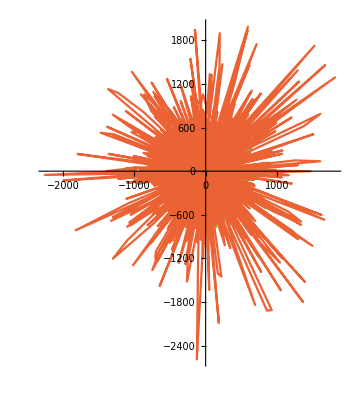

```mathematica
PolarPlot[Out[23],{θ,1,100}]
```

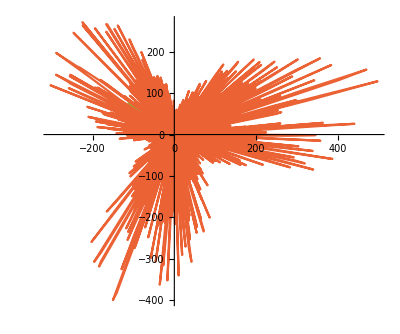

```mathematica
PolarPlot[Out[23],{θ,1,20}]
```

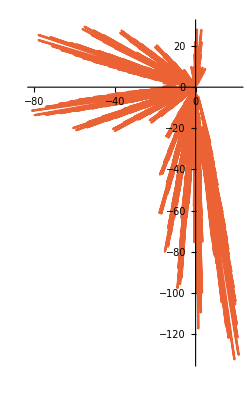

```mathematica
PolarPlot[Out[23],{θ,1,5}]
```

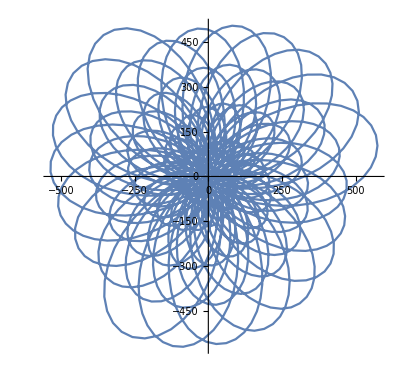

```mathematica
PolarPlot[(1+3 θ) (1+1/2 (-1-Cos[θ π]))+1/4 θ(1+Cos[θ π]),{θ,1,200}]
```

```mathematica
?*Curve
```

```mathematica
KochCurve[2]
```

Line[{{0.,0.},{0.111111,0.},{0.166667,0.096225},{0.222222,0.},{0.333333,0.},{0.388889,0.096225},{0.333333,0.19245},{0.444444,0.19245},{0.5,0.288675},{0.555556,0.19245},{0.666667,0.19245},{0.611111,0.096225},{0.666667,0.},{0.777778,0.},{0.833333,0.096225},{0.888889,0.},{1.,0.}}]

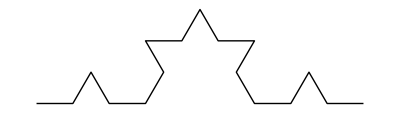

```mathematica
Graphics[KochCurve[2]]
```

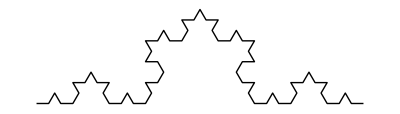

```mathematica
Graphics[KochCurve[3]]
```

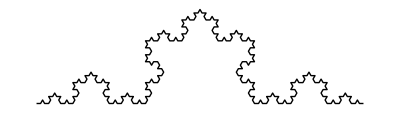

```mathematica
Graphics[KochCurve[4]]
```

```mathematica
g[x,n]
```

g[x,n]

```mathematica
D[g[x,n], n]
```

g^(0,1)[x,n]

```mathematica
D[g[x,Subscript[n, f]], n]
```

g^(0,1)[x,n_f] Subscript^(1,0)[n,f]

```mathematica
x^2
```

x^2

```mathematica
g[x_]:=x^2
```

```mathematica
g[g[x]]
```

x^4

```mathematica
(g^n)[x]
```

g^n[x]

```mathematica
y[x,n]
```

y[x,n]

```mathematica
r[x,n]
```

r[x,n]

```mathematica
r'[x,Subscript[n, f]]==0
```

r'[x,n_f]==0

```mathematica
D[h[x],{x,-3}]
```

D::dvar: Multiple derivative specifier {x,-3} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

∂_{x,-3} h[x]

```mathematica
D[h[x],{x,3}]
```

h^(3)[x]

```mathematica
D[x^(2 n),n]
```

2 x^(2 n) Log[x]

```mathematica
D[x^(2 n),n]/.x->1
```

0

```mathematica
D[a^(2 n),n]
```

2 a^(2 n) Log[a]

```mathematica
D[2^(2 n),n]
```

2^(1+2 n) Log[2]

```mathematica
Plot3D[2 x^(2 n) Log[x],{x,-2,2},{n,1,10}]
```

-Graphics3D-

```mathematica
Plot3D[2 x^(2 n) Log[x],{x,-2,2},{n,1,4}]
```

-Graphics3D-

```mathematica
Plot3D[2 x^(2 n) Log[x],{x,0,2},{n,1,4}]
```

-Graphics3D-

```mathematica
Solve[2 x^(2 n) Log[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1},{x→0^(1/n)}}

```mathematica
Exp[x]==x^(x/Log[x])
```

ⅇ^x==x^(x/Log[x])

```mathematica
FindInstance[ⅇ^x==x^(x/Log[x]),{x}]
```

{{x→171/10-(103 ⅈ)/5}}

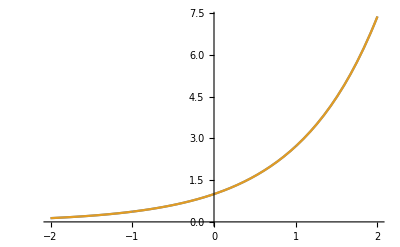

```mathematica
Plot[{ⅇ^x,x^(x/Log[x])},{x,-2,2}]
```

```mathematica
Exp[x]==x
```

ⅇ^x==x

```mathematica
Reduce[ⅇ^x==x]
```

C[1]∈ℤ&&x==-ProductLog[C[1],-1]

```mathematica
Exp[-ProductLog[1,-1]]
```

ⅇ^(-ProductLog[1,-1])

```mathematica
N[ⅇ^(-ProductLog[1,-1])]
```

2.06228-7.58863 ⅈ